# EWS Analysis of Fish Model

## Setup

```mathematica
(* Set Directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fish_project"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};

(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* Import user-defined functions *)
Get["/Users/tbury/Library/Mobile Documents/com~apple~CloudDocs/Mathematica/packages/my_functions/spectral_functions.wl"];
```

```mathematica
(* Figure display parameters *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={60,50,20,20};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos={0.035,0.86} ;(* panel letter label *)

numRealisations=100;
```

## Simulate Ricker Model

### Parameters

```mathematica
(* model baseline parameter values *)
k=10; (* carrying capacity *)
p=2;(* exponent for sigmoid functional response *)
h=0.75; (* half-saturation rate *)
r=0.75; (* growth rate *)
f=0; (* grazing rate *)
x0=10; (* initial condition *)
se=0.05;(* environmental noise *)
tmax=400; (* number of time steps *)
```

```mathematica
(* set up array for series data *)
expSeries=ConstantArray[0,{numRealisations,tmax+1}];
trunSeries=ConstantArray[0,{numRealisations,tmax+1}];
```

### Discrete dynamical system

```mathematica
(* N_t+1 = f(N_t) *)
Clear[fun]
fun[r_,k_,f_,h_,noise_,pop_]:=pop*Exp[r(1-pop/k)+se noise]-f pop^2 / (pop^2+h^2)
```

### Simulate exploitation scenario

```mathematica
(* range of grazing rates to increment through *)
fVals=Subdivide[0,3,tmax];
```

```mathematica
For[i=1,i≤numRealisations,i++,
(* array for trajectory *)
x=ConstantArray[0,tmax+1];
(* set initial condition *)
x[[1]]=10;
(* normal random variables mean zero variance 1 for noise *)
noise=RandomVariate[NormalDistribution[0,1],tmax];
(* begin simulation *)
For[q=1,q≤tmax-1,q++,
f=fVals[[q]];
x[[q+1]]=fun[r,k,f,h,noise[[q]],x[[q]]];
(* don't let x go negative *)
If[x[[q+1]]<0,
x[[q+1]]==0;];
];
(* add trajectory to series array *)
expSeries[[i,;;]]=x;
]
```

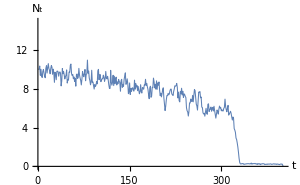

```mathematica
(* single realisation plot *)
plotSingleExp=ListLinePlot[expSeries[[4]],
ImageSize->300,
PlotStyle->Thickness[0.0025],
PlotRange->{0,15},
LabelStyle->14,
AxesLabel->{"t","N_t"}]
```

### Simulate truncation scenario

```mathematica
(* set grazing rate and exploitation fate *)
f=0;
rVals=Subdivide[0.5,2.6,tmax];
```

```mathematica
For[i=1,i≤numRealisations,i++,
(* array for trajectory *)
x=ConstantArray[0,tmax+1];
(* set initial condition *)
x[[1]]=10;
(* normal random variables mean zero variance 1 for noise *)
noise=RandomVariate[NormalDistribution[0,1],tmax];
(* begin simulation *)
For[q=1,q≤tmax,q++,
r=rVals[[q]];
x[[q+1]]=fun[r,k,f,h,noise[[q]],x[[q]]];
(* don't let x go negative *)
If[x[[q+1]]<0,
x[[q+1]]==0;];
];
(* add trajectory to series array *)
trunSeries[[i,;;]]=x;
]
```

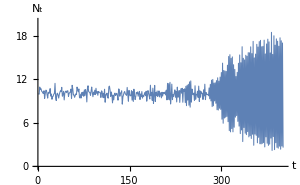

```mathematica
(* single realisation plot *)
plotSingleTrun=ListLinePlot[trunSeries[[6]],
ImageSize->300,
PlotStyle->Thickness[0.0025],
PlotRange->{0,20},
LabelStyle->14,
AxesLabel->{"t","N_t"}]
```

## Exploitation scenario - traditional indicators

### Key values / parameters

```mathematica
(* control parameter range *)
fl=0;
fh=3;
(* saddle node bifurcation values *)
fcrit1=2.364; 
fcrit2=1.491;
(* transition time make prebifTime yrs less than bifurcation to account for noise *)
prebifTime=10;
tcritExp=Floor[(fcrit1-fl)*tmax /(fh-fl)]-prebifTime;

(* details on EWS *)
detrendOp=1;
bandWidth=0.5; (* for Gaussian filter (fraction of timeseries) *)
rollWindow=0.25; (* rolling window for stat metrics (fraction of timeseries *)
tauVals={1,2}; (* lag times for autocorrelation *)

(* plot parameters *)
aHeadSize=0.03;
```

### Detrending Process (Gaussian Filter)

```mathematica
(* Detrend data up to transition *) 
tVals=Range[0,tmax];
dataFitExp=If[detrendOp==1,
Table[
GaussianFilter[expSeries[[i,1;;tcritExp]],tcritExp*bandWidth],
{i,1,numRealisations}],
ConstantArray[0,{numRealisations,tcritExp}]
];
```

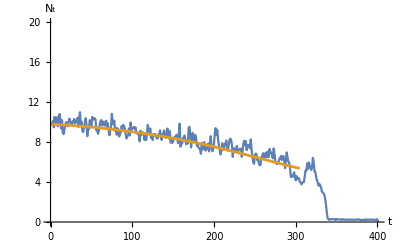

```mathematica
(* plot of single realisation *)
plotNum=1;
ListLinePlot[{expSeries[[plotNum]],dataFitExp[[plotNum]]},
ImageSize->400,
LabelStyle->14,
AxesLabel->{"t","N_t"},
PlotRange->{{0,tmax},{0,20}},
PlotStyle->{Default,Thickness[0.005]},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

```mathematica
(* compute residuals of series *)
residualsExp=expSeries[[1;;numRealisations,1;;tcritExp]]-dataFitExp;
```

### Variance

```mathematica
(* number of component in the rolling window *)
windowComps=Floor[rollWindow*Length[tVals]];
varSeries=Table[MovingMap[Variance,residualsExp[[i]],windowComps],{i,1,numRealisations}];
meanSeries=Table[MovingMap[Mean,expSeries[[i,1;;tcritExp]],windowComps],{i,1,numRealisations}];
cvSeries = varSeries/meanSeries;
```

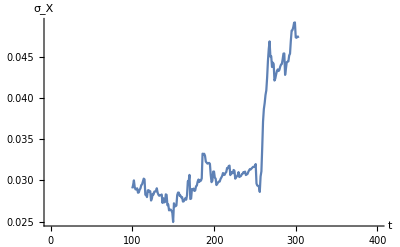

```mathematica
(* single plot *)
ListPlot[{tVals[[windowComps+1;;tcritExp]],cvSeries[[2]]}ᵀ, (* to account for the rolling window *)
Joined->True,
AxesLabel->{"t","σ_X"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},Automatic}]
```

```mathematica
(* Over all simulations *)
meanCVseries=Mean[cvSeries];
devCVseries=StandardDeviation[cvSeries];
```

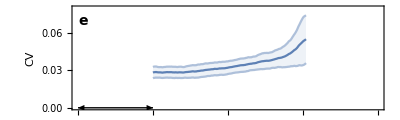

```mathematica
cvPlotExp=ListPlot[{{tVals[[windowComps+1;;tcritExp]],meanCVseries}ᵀ,
{tVals[[windowComps+1;;tcritExp]],meanCVseries+devCVseries}ᵀ,
{tVals[[windowComps+1;;tcritExp]],meanCVseries-devCVseries}ᵀ},
Joined->True,
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5]},
Filling->{{2->{1}},{3->{1}}},
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},{0,0.08}},
FrameLabel->{{"CV",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
(*FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5},Automatic},{Automatic,Automatic}}*)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
Text[Style["e",14,Bold],Scaled[labelLetterPos]]}]
```

### Autocorrelation of Residuals at various lags

```mathematica
(* form [a1;a2;,,,;an] *)
acSeries=Table[MovingMap[CorrelationFunction[#,tauVals[[j]]]&,residualsExp[[i]],windowComps],{i,1,numRealisations},{j,1,Length[tauVals]}]; 
acSeries//Dimensions
(* sim number, lag number, time value *)
```

$Aborted

{}

```mathematica
(* line legend *)
legend=LineLegend[TMBcolours[[1;;2]],{"τ=1","τ=2"}]
```

```mathematica
(* plot *)
acPlot=ListPlot[Table[{tVals[[windowComps+1;;tcritExp]],acSeries[[1,j]]}ᵀ,{j,1,Length[tauVals]}],
Joined->True,
AxesLabel->{"t","AR(1)"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},All},
PlotLegends->Placed[legend,{0.2,0.7}]];
```

```mathematica
(* a plot averaged over simulations *)
meanACseries=Table[Mean[acSeries[[;;,j]]],{j,1,Length[tauVals]}];
devACseries=If[numRealisations>1,Table[StandardDeviation[acSeries[[;;,j]]],{j,1,Length[tauVals]}],
ConstantArray[0,Length[meanACseries]]];
meanACseries//Dimensions
```

{2,205}

```mathematica
(* ac plot as a function of lag *)
Clear[acPlot];
acPlot[j_]:=ListPlot[{
{tVals[[windowComps+1;;tcritExp]],meanACseries[[j]]}ᵀ,
{tVals[[windowComps+1;;tcritExp]],meanACseries[[j]]+devACseries[[j]]}ᵀ,
{tVals[[windowComps+1;;tcritExp]],meanACseries[[j]]-devACseries[[j]]}ᵀ},
Joined->True,
PlotStyle->{TMBcolours[[j]],Lighter[TMBcolours[[j]],0.5],Lighter[TMBcolours[[j]],0.5]},
Filling->{{2->{1}},{3->{1}}},
LabelStyle->14,
Frame->True,
FrameLabel->{{"AC",""},{"",""}},
PlotRange->{{0,tmax},{-0.1,1}},
PlotRangeClipping->False,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
PlotLegends->If[j==1,Placed[legend,{0.12,0.7}],None]];
```

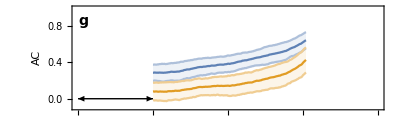

```mathematica
acPlotLagsExp=Show[Table[acPlot[i],{i,1,Length[tauVals]}],
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
Ticks->{Default,{0,0.4,0.8}},
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
(*Text[Style["t",14],Scaled[{1.04,-0.05}]]*)
Text[Style["g",14,Bold],Scaled[labelLetterPos]]}]
```

## Exploitation scenario - spectral metrics

#### Parameters

```mathematica
psdWindowSize=windowComps; (* rolling window size for psd computation *)
hamLength=40; (* Length of Hamming window to compute psd within rolling window (as a proportion) *)
hamOffset=20; (* overlap of Hamming window *)
psdTime=250; (* time to evaluate psd for figure *)
```

#### Compute PSD over a rolling window

```mathematica
(* evaluate power spectrum of residuals in rolling window *)
windowComps=Floor[rollWindow*Length[tVals]];
pSpecSeries=Table[MovingMap[TBPowerSpecWelch[{#,1,hamLength,hamOffset}]&,residualsExp[[i]],windowComps],{i,1,numRealisations}];
ωVals=pSpecSeries[[1,1,1]];
```

```mathematica
residualsExp//Dimensions
```

{100,305}

```mathematica
(* number of realisations, number of time steps, {omega values, psd values} *)
pSpecSeries//Dimensions
```

{100,205,2,41}

```mathematica
(* Find averaging properties at time psdTime *)
meanPsd=Mean[pSpecSeries[[;;,psdTime-windowComps,2]]];
devPsd=StandardDeviation[pSpecSeries[[;;,psdTime-windowComps,2]]];
```

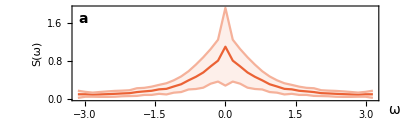

```mathematica
psdAvExp=ListPlot[{{ωVals,meanPsd}//Transpose,
{ωVals,meanPsd+devPsd}//Transpose,
{ωVals,meanPsd-devPsd}//Transpose},
Joined->True,
Frame->True,
Filling->{{2->{1}},{3->{1}}},
LabelStyle->14,
PlotRange->{{-Pi,Pi},All},
PlotStyle->{TMBcolours⟦4⟧,Lighter[TMBcolours⟦4⟧,0.5],Lighter[TMBcolours⟦4⟧,0.5]},
FrameLabel->{{"S(ω)",""},{"",""}},
(*FrameTicks->{{Transpose[{Range[0,0.01,0.002],Range[0,10,2]}],Automatic},{Automatic,Automatic}}*)
PlotRangeClipping->False,
Epilog->{(*Text[Style["×10^-3",14],indexPos]*)
Text[Style["ω",14],labelPos],
Text[Style["a",14,Bold],Scaled[labelLetterPos]]},
ImageSize->400,
AspectRatio->0.3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

#### Compute Coherence Factor from Power Spectra

```mathematica
pSpecSeries//Dimensions
```

{100,205,2,41}

```mathematica
?TBCoherFactor
```

TBCoherFactor[{freqVals,powerVals}] computes the coherence factor of the given power specrum
output = coherenceFactor
Coherence factor is computed as CF=H/W where H is the height of the peak in spectrum and W is the relative width given by the width at half the height of the peak divided by the frequency that gives the peak

```mathematica
(* compute coherence factors *)
coherFactorSeries=Table[TBCoherFactor[pSpecSeries[[i,j]]],{i,1,numRealisations},{j,1,Dimensions[pSpecSeries]⟦2⟧}];
```

```mathematica
coherFactorSeries//Dimensions
```

{100,205}

```mathematica
(* a plot averaged over simulations *)
meanCoherSeries=Mean[coherFactorSeries];
devCoherSeries=StandardDeviation[coherFactorSeries];

(* quantiles *)
quantile25Coher=Quantile[coherFactorSeries,0.25];
medianCoher=Quantile[coherFactorSeries,0.5];
quantile75Coher=Quantile[coherFactorSeries,0.75];
```

```mathematica
quantile75Coher//Dimensions
```

{205}

```mathematica
tVals[[windowComps+1;;tcritExp]]//Dimensions
```

{205}

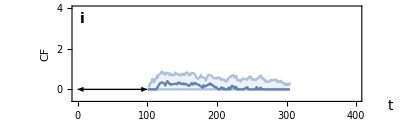

```mathematica
coherSeriesPlot=ListPlot[{{tVals[[windowComps+1;;tcritExp]],quantile25Coher}ᵀ,
{tVals[[windowComps+1;;tcritExp]],quantile75Coher}ᵀ,{tVals[[windowComps+1;;tcritExp]],medianCoher}ᵀ},
Joined->True,
PlotStyle->{Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5],TMBcolours⟦1⟧},
Filling->{{1->{3}},{2->{3}}},
LabelStyle->14,
Frame->{{True,False},{True,True}},
PlotRange->{{0,tmax},{-0.5,4}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameLabel->{{"CF",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
(*FrameTicks->{{{{0,0},{0.004,4},{0.008,8},{0.012,12},{0.016,16},{0.02,20}},Automatic},{Automatic,Automatic}}*)
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Axes->False,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
(*Text[Style["×10^-3",14,TMBcolours[[1]]],indexPos]*)
Text[Style["t",14],Scaled[{1.1,-0.05}]],
Text[Style["i",14,Bold],Scaled[labelLetterPos]]}]
```

#### Compute AIC weights from power spectra

```mathematica
pSpecSeries//Dimensions
```

{100,205,2,41}

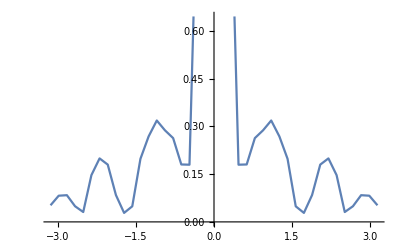

```mathematica
ListLinePlot[Transpose[pSpecSeries[[1,150]]]]
```

```mathematica
pSpecSeries[[1,150]]
```

{{-π,-(19 π)/20,-(9 π)/10,-(17 π)/20,-(4 π)/5,-(3 π)/4,-(7 π)/10,-(13 π)/20,-(3 π)/5,-(11 π)/20,-π/2,-(9 π)/20,-(2 π)/5,-(7 π)/20,-(3 π)/10,-π/4,-π/5,-(3 π)/20,-π/10,-π/20,0,π/20,π/10,(3 π)/20,π/5,π/4,(3 π)/10,(7 π)/20,(2 π)/5,(9 π)/20,π/2,(11 π)/20,(3 π)/5,(13 π)/20,(7 π)/10,(3 π)/4,(4 π)/5,(17 π)/20,(9 π)/10,(19 π)/20,π},{0.0522133,0.0823493,0.0839842,0.0492201,0.0310547,0.147003,0.199654,0.180121,0.0844237,0.0283079,0.0490308,0.198327,0.26876,0.318827,0.287928,0.26347,0.180598,0.179831,1.12074,2.73023,2.01209,2.73023,1.12074,0.179831,0.180598,0.26347,0.287928,0.318827,0.26876,0.198327,0.0490308,0.0283079,0.0844237,0.180121,0.199654,0.147003,0.0310547,0.0492201,0.0839842,0.0823493,0.0522133}}

```mathematica
TBHopfAIC[pSpecSeries[[1,150]]]//Timing
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{0.128981,0.475999}

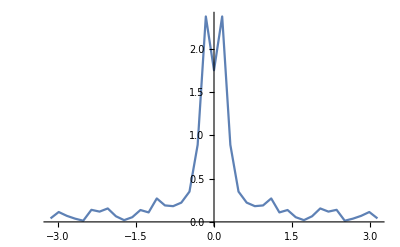

```mathematica
ListLinePlot[Transpose[pSpecSeries[[1,140]]],PlotRange->All]
```

```mathematica
(* compute AIC weights - LONG SIMULATION *)
aicWeightSeriesExp=Monitor[
Table[Quiet[TBHopfAIC[pSpecSeries[[i,j]]]],{i,1,numRealisations},{j,1,Dimensions[pSpecSeries]⟦2⟧}],
{ProgressIndicator[i,{1,numRealisations}],ProgressIndicator[j,{1,Dimensions[pSpecSeries][[2]]}]}];
```

```mathematica
(* export data *)
Export["data/sim_data/aicWeightsExp.csv",aicWeightSeriesExp];
```

```mathematica
(*(* import aic weight data *)
aicWeightSeriesExp=Import["data/sim_data/aicWeightsExp.csv"];*)
```

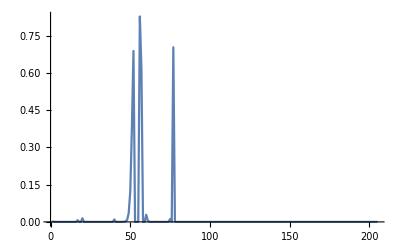

```mathematica
ListLinePlot[aicWeightSeriesExp[[7]],PlotRange->All]
```

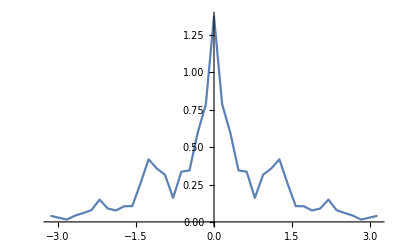

```mathematica
ListLinePlot[Transpose[pSpecSeries[[1,-10]]],PlotRange->All]
```

```mathematica
aicWeightSeriesExp//Dimensions
```

{100,205}

```mathematica
coherFactorSeries//Dimensions
```

{100,205}

```mathematica
(* a plot averaged over simulations *)
meanAICSeries=Mean[aicWeightSeriesExp];
devAICSeries=StandardDeviation[aicWeightSeriesExp];
```

```mathematica
(* quantiles *)
quantile25aicWeights=Quantile[aicWeightSeriesExp,0.25];
medianaicWeights=Quantile[aicWeightSeriesExp,0.5];
quantile75aicWeights=Quantile[aicWeightSeriesExp,0.75];
```

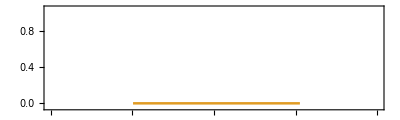

```mathematica
aicWeightSeriesPlot=ListPlot[{{tVals[[windowComps+1;;tcritExp]],quantile25aicWeights}ᵀ,
{tVals[[windowComps+1;;tcritExp]],quantile75aicWeights}ᵀ,{tVals[[windowComps+1;;tcritExp]],medianaicWeights}ᵀ},
Joined->True,
PlotStyle->{Lighter[TMBcolours⟦2⟧,0.5],Lighter[TMBcolours⟦2⟧,0.5],TMBcolours⟦2⟧},
Filling->{{1->{3}},{2->{3}}},
LabelStyle->14,
PlotRange->{{0,tmax},{-0.05,1.05}},
Frame->{{False,True},{True,True}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameLabel->{{"","w_AIC"},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,All},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Axes->False]
```

```mathematica
psdMetricExpPlot=Overlay[{coherSeriesPlot,aicWeightSeriesPlot}]
```

-Graphics--Graphics-

#### Compute AIC weights with fixed ω0

```mathematica
(*pSpecSeries//Dimensions*)
```

```mathematica
(*ω0Choose=1;*)
```

```mathematica
(*(* compute AIC weights - LONG SIMULATION *)
aicWeightSeries=Table[Quiet[TBFitSpecFixW[pSpecSeries[[i,j]],ω0Choose]]⟦1⟧,{i,1,numRealisations},{j,1,Dimensions[pSpecSeries]⟦2⟧}];
Export["data/sim_data/aicWeightsExpWFix.csv",aicWeightSeries];*)
```

```mathematica
(*(* import aic weight data *)
aicWeightSeries=Import["data/sim_data/aicWeightsExpWFix.csv"];*)
```

```mathematica
(*aicWeightSeries//Dimensions*)
```

```mathematica
(*(* a plot averaged over simulations *)
meanAICSeries=Mean[aicWeightSeries];
devAICSeries=StandardDeviation[aicWeightSeries];*)
```

```mathematica
(*(* quantiles *)
quantile25aicWeights=Quantile[aicWeightSeries,0.25];
medianaicWeights=Quantile[aicWeightSeries,0.5];
quantile75aicWeights=Quantile[aicWeightSeries,0.75];*)
```

```mathematica
(*aicWeightSeriesPlot=ListPlot[{{tVals[[windowComps+1;;tcritExp]],quantile25aicWeights}ᵀ,
{tVals[[windowComps+1;;tcritExp]],quantile75aicWeights}ᵀ,{tVals[[windowComps+1;;tcritExp]],medianaicWeights}ᵀ},
Joined->True,
PlotStyle->{Lighter[TMBcolours⟦2⟧,0.5],Lighter[TMBcolours⟦2⟧,0.5],TMBcolours⟦2⟧},
Filling->{{1->{3}},{2->{3}}},
LabelStyle->14,
PlotRange->{{0,tmax},{-0.4,1.05}},
Frame->{{False,True},{True,True}},
Axes->{False,False},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameLabel->{{"","w_AIC"},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Range[0,1,0.25]},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3]*)
```

```mathematica
(*psdMetricExpPlot=Overlay[{coherSeriesPlot,aicWeightSeriesPlot}]*)
```

## Bifurcation Diagram (exploited pop)

Deterministic model is
N_(t+1)=N_t e^(r(1-N_t/K))-F N_t^2/(N_t^2+h^2)

### Specifications

```mathematica
Import["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fish_project/bifurcation/fish_exp.dat"];
```

```mathematica
(* Import data *)
rawdata=Import["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fish_project/bifurcation/fish_exp.dat"];

(* plotting spec *)
lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{0,3},{0,20}}; (* plot range *)
(*frLabel={"F","N"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of F *)
fbifVals=fulldata[[;;,1]];
tbifVals=(fbifVals-fl)*tmax /(fh-fl);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
(*nodeSections[[3]]=Cases[nodeSections[[3]],{x_,_,_,_}/; x>0] ; 
nodeSections=Append[nodeSections,Cases[nodeSections[[6]],{_,x_,_,_}/;x>0]];
nodeSections[[6]]=Cases[nodeSections[[6]],{_,x_,_,_}/;x<0]; *)(* had to seperate out branches for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}]
```

{2,1,2,1}

```mathematica
(* Take relevant branches of node sections *)
delList={};
branchesNums=Complement[Range[1,numBranches],delList]
```

{1,2,3,4}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

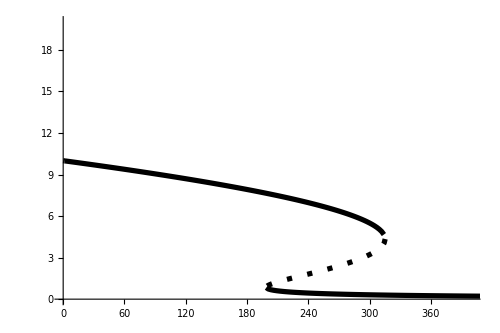

```mathematica
(* Make plot *)
bifPlotExp=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,tmax},{0,20}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Incorporate bif diagram with Simulation

```mathematica
arLength=windowComps;
lineStyle={TMBcolours[[4]],Opacity[1]};
sqHeight=2;
sqCenter=7;
```

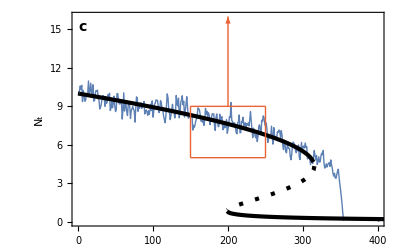

```mathematica
(* Incorporate with simulation *)
figBifTrajExp=Show[{plotSingleExp,bifPlotExp},
PlotRange->{{0,tmax},{0,16}},
LabelStyle->14,
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom-5,padTop-5}},
FrameLabel->{{"N_t",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["c",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle],
Line[{{psdTime,-sqHeight+sqCenter},{psdTime,sqHeight+sqCenter}}],
Line[{{psdTime-windowComps,-sqHeight+sqCenter},{psdTime-windowComps,sqHeight+sqCenter}}],
Line[{{psdTime-windowComps,sqHeight+sqCenter},{psdTime,sqHeight+sqCenter}}],
Line[{{psdTime-windowComps,-sqHeight+sqCenter},{psdTime,-sqHeight+sqCenter}}],
Arrow[{{psdTime-windowComps/2,sqHeight+sqCenter},{psdTime-windowComps/2,16}}]}]
```

## Truncation scenario - traditional indicators

### Key values / parameters

```mathematica
(* control parameter range *)
rl=0.5;
rh=2.6;
(* PD bifurcation values *)
rcrit1=2; 
rcrit2=2.526;
(* transition times *)
tcritTrun=Floor[(rcrit1-rl)*tmax /(rh-rl)];

(* details on EWS *)
detrendOp=1;
bandWidth=0.2; (* for Gaussian filter (fraction of timeseries) *)
rollWindow=0.25; (* rolling window for stat metrics (fraction of timeseries *)
tauVals={1,2}; (* lag times for autocorrelation *)

(* plot parameters *)
aHeadSize=0.03;
```

### Detrending Process (Gaussian Filter)

```mathematica
(* Detrend data up to transition *) 
tVals=Range[1,tmax];
dataFitTrun=If[detrendOp==1,
Table[
GaussianFilter[trunSeries[[i,1;;tcritTrun]],tcritTrun*bandWidth],
{i,1,numRealisations}],
ConstantArray[0,{numRealisations,tcritTrun}]
];
```

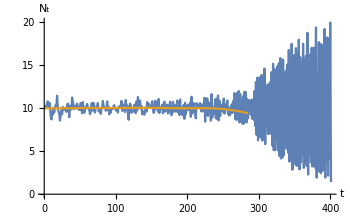

```mathematica
(* plot of single realisation *)
plotNum=1;
ListLinePlot[{trunSeries[[plotNum]],dataFitTrun[[plotNum]]},
ImageSize->350,
LabelStyle->14,
AxesLabel->{"t","N_t"},
PlotRange->{{0,tmax},{0,20}},
PlotStyle->{Default,Default},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

```mathematica
dataFitTrun//Dimensions
```

{100,285}

```mathematica
trunSeries[[;;,1;;tcritTrun]]//Dimensions
```

{100,285}

```mathematica
(* compute residuals of series *)
residualsTrun=trunSeries[[1;;numRealisations,1;;tcritTrun]]-dataFitTrun;
```

### Variance

```mathematica
(* number of component in the rolling window *)
windowComps=Floor[rollWindow*Length[tVals]];
varSeries=Table[MovingMap[Variance,residualsTrun[[i]],windowComps],{i,1,numRealisations}];
meanSeries=Table[MovingMap[Mean,trunSeries[[i,1;;tcritTrun]],windowComps],{i,1,numRealisations}];
cvSeries = varSeries/meanSeries;
```

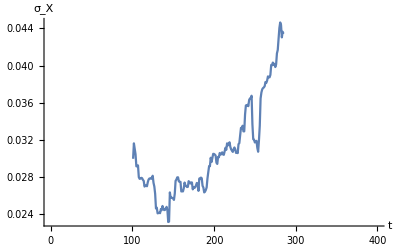

```mathematica
(* single plot *)
ListPlot[{tVals[[windowComps+1;;tcritTrun]],cvSeries[[2]]}ᵀ, (* to account for the rolling window *)
Joined->True,
AxesLabel->{"t","σ_X"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},Automatic}]
```

```mathematica
(* Over all simulations *)
meanCVseries=Mean[cvSeries];
devCVseries=StandardDeviation[cvSeries];
```

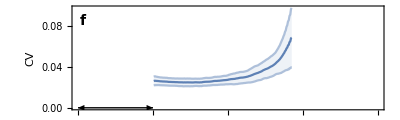

```mathematica
cvPlotTrun=ListPlot[{{tVals[[windowComps+1;;tcritTrun]],meanCVseries}ᵀ,
{tVals[[windowComps+1;;tcritTrun]],meanCVseries+devCVseries}ᵀ,
{tVals[[windowComps+1;;tcritTrun]],meanCVseries-devCVseries}ᵀ},
Joined->True,
PlotStyle->{TMBcolours⟦1⟧,Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5]},
Filling->{{2->{1}},{3->{1}}},
LabelStyle->14,
Frame->True,
PlotRange->{{0,tmax},All},
FrameLabel->{{"CV",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
(*FrameTicks->{{{{0,0},0.2,0.4,0.6,0.8},Automatic},{Automatic,Automatic}}*)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
Text[Style["f",14,Bold],Scaled[labelLetterPos]]}]
```

### Autocorrelation of Residuals at various lags

```mathematica
(* form [a1;a2;,,,;an] *)
acSeries=Table[MovingMap[CorrelationFunction[#,tauVals[[j]]]&,residualsTrun[[i]],windowComps],{i,1,numRealisations},{j,1,Length[tauVals]}]; 
acSeries//Dimensions
(* sim number, lag number, time value *)
```

$Aborted

{100,2,185}

```mathematica
(* line legend *)
legend=LineLegend[TMBcolours[[1;;2]],{"τ=1","τ=2"}]
```

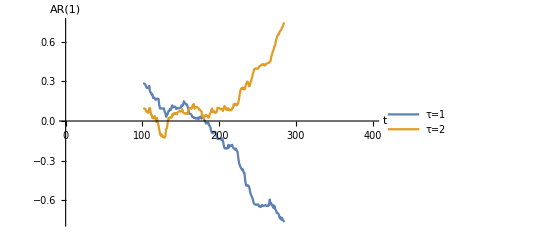

```mathematica
(* plot *)
acPlot=ListPlot[Table[{tVals[[windowComps+1;;tcritTrun]],acSeries[[1,j]]}ᵀ,{j,1,Length[tauVals]}],
Joined->True,
AxesLabel->{"t","AR(1)"},
LabelStyle->14,
ImageSize->400,
PlotRange->{{0,tmax},All},
PlotLegends->Placed[legend,{0.2,0.7}]]
```

```mathematica
(* a plot averaged over simulations *)
meanACseries=Table[Mean[acSeries[[;;,j]]],{j,1,Length[tauVals]}];
devACseries=If[numRealisations>1,Table[StandardDeviation[acSeries[[;;,j]]],{j,1,Length[tauVals]}],
ConstantArray[0,Length[meanACseries]]];
meanACseries//Dimensions
```

{2,185}

```mathematica
(* ac plot as a function of lag *)
Clear[acPlot];
acPlot[j_]:=ListPlot[{
{tVals[[windowComps+1;;tcritTrun]],meanACseries[[j]]}ᵀ,
{tVals[[windowComps+1;;tcritTrun]],meanACseries[[j]]+devACseries[[j]]}ᵀ,
{tVals[[windowComps+1;;tcritTrun]],meanACseries[[j]]-devACseries[[j]]}ᵀ},
Joined->True,
PlotStyle->{TMBcolours[[j]],Lighter[TMBcolours[[j]],0.5],Lighter[TMBcolours[[j]],0.5]},
Filling->{{2->{1}},{3->{1}}},
LabelStyle->14,
Frame->True,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
FrameLabel->{{"AC",""},{"",""}},
PlotRange->{{0,tmax},All},
PlotRangeClipping->False,
PlotLegends->If[j==1,Placed[legend,{0.12,0.24}],None]];
```

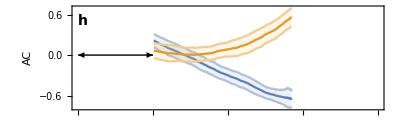

```mathematica
acPlotLagsTrun=Show[Table[acPlot[i],{i,1,Length[tauVals]}],
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
PlotRange->{{0,tmax},All},
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
(*Text[Style["t",14],Scaled[{1.03,-0.05}]]*)
Text[Style["h",14,Bold],Scaled[labelLetterPos]]}]
```

## Truncation scenario - spectral properties

#### Parameters

```mathematica
psdWindowSize=windowComps; (* rolling window size for psd computation *)
hamLength=40; (* Length of Hamming window *)
hamOffset=20; (* Offset of Hamming window *)
```

#### Using a single time frame

```mathematica
(* structure of residuals (realisation number, time step) *)
residualsTrun//Dimensions
```

{100,285}

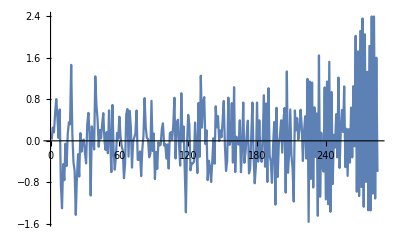

```mathematica
(* plot of residuals in first time frame *)
ListLinePlot[{residualsTrun[[1]]},PlotRange->All]
```

```mathematica
(*(* discard trajectories that have already transitioned *)
residualsSt=DeleteCases[residualsFold,a_/;a[[psdTime+10]]<0];
residualsSt//Length*)
```

```mathematica
?TBPowerSpecWelch
```

{freqVals,pSpec} = TBPowerSpecWelch[{yVals,dt,hamLength,hamOffset}] estimates the power spectrum usign Welch's method.
This involves computing the periodogram with overlapping Hamming windows.
hamLength: number of data points in Hamming window, or if in (0,1) taken as a proportion of total data input
hamOffset: number of data points to offset the window by on each interation, or if in (0,1) taken as a proportion of Hamming window size

```mathematica
(* evaluate power spectrum of residuals at a particular time *)
psdTime=250;
pSpecWelch=TBPowerSpecWelch[{residualsTrun[[1,psdTime-psdWindowSize;;psdTime]],1,hamLength,hamOffset}];
pSpec=TBPowerSpec[{residualsTrun[[1,psdTime-psdWindowSize;;psdTime]],1}];
```

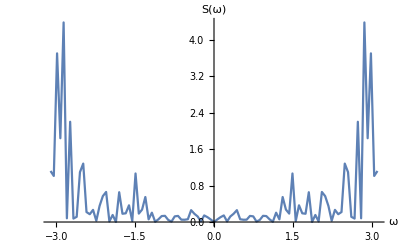

```mathematica
pSpecPlot=ListLinePlot[Transpose[pSpec],
PlotRange->All,
PlotStyle->{PointSize[0.01]},
LabelStyle->12,
AxesLabel->{"ω","S(ω)"},
PlotRangeClipping->False]
```

```mathematica
(* compute coherence factor *)
?TBCoherFactor
```

TBCoherFactor[{freqVals,powerVals}] computes the coherence factor of the given power specrum
output = coherenceFactor
Coherence factor is computed as CF=H/W where H is the height of the peak in spectrum and W is the relative width given by the width at half the height of the peak divided by the frequency that gives the peak

```mathematica
TBCoherFactor[pSpecWelch]
```

2.2736

```mathematica
(* compute aic score *)
?TBFitSpec
```

TBFitSpec[pSpec] fits the unimodal and bimodal power specrums that occur preceding a Fold and a Hopf bifurcation respectively to the provided power spectrum.
pSpec = {freqVals,powerVals}
Outputs {hopfAICweight,rSquaredRatio,cUni,λUni,cBi,λBi,ω0Bi}
AIC weights can be interpreted as the probability that the fitted model is the best model (in the AIC sense)
RSquared ratio is R^2 of Fold divided by R^2 of Hopf
c is the noise parameter
λ is the absolute value of the dominant eigenvalue
ω0 is the intrinsic frequency
as found in each of the fitted power spectra

```mathematica
TBFitSpec[pSpecWelch]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{1.,0.447575,553669.,1044.99,0.170432,-0.280192,2.98455}

#### Compute PSD over a rolling window

```mathematica
(* evaluate power spectrum of residuals in rolling window *)
windowComps=Floor[rollWindow*Length[tVals]];
pSpecSeries=Table[MovingMap[TBPowerSpecWelch[{#,1,hamLength,hamOffset}]&,residualsTrun[[i]],windowComps],{i,1,numRealisations}];
ωVals=pSpecSeries[[1,1,1]];
```

```mathematica
residualsTrun//Dimensions
```

{100,285}

```mathematica
(* number of realisations, number of time steps, {omega values, psd values} *)
pSpecSeries//Dimensions
```

{100,185,2,41}

```mathematica
(* Find averaging properties at time psdTime *)
meanPsd=Mean[pSpecSeries[[;;,psdTime-windowComps,2]]];
devPsd=StandardDeviation[pSpecSeries[[;;,psdTime-windowComps,2]]];
```

```mathematica
(* extend the power spectrum using periodicity *)
ωExt=Join[ωVals-2Pi,ωVals,ωVals+2Pi];
meanPsdExt=Join[meanPsd,meanPsd,meanPsd];
devPsdExt=Join[devPsd,devPsd,devPsd];
cutSeries=23;
```

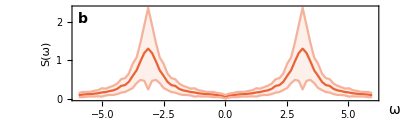

```mathematica
psdAvTrun=ListPlot[{{ωExt[[cutSeries;;-cutSeries]],meanPsdExt[[cutSeries;;-cutSeries]]}//Transpose,
{ωExt[[cutSeries;;-cutSeries]],meanPsdExt[[cutSeries;;-cutSeries]]+devPsdExt[[cutSeries;;-cutSeries]]}//Transpose,
{ωExt[[cutSeries;;-cutSeries]],meanPsdExt[[cutSeries;;-cutSeries]]-devPsdExt[[cutSeries;;-cutSeries]]}//Transpose},
Joined->True,
Frame->True,
Filling->{{2->{1}},{3->{1}}},
LabelStyle->14,
PlotRange->{{-6,6},All},
PlotStyle->{TMBcolours⟦4⟧,Lighter[TMBcolours⟦4⟧,0.5],Lighter[TMBcolours⟦4⟧,0.5]},
FrameLabel->{{"S(ω)",""},{"",""}},
(*FrameTicks->{{Transpose[{Range[0,0.01,0.002],Range[0,10,2]}],Automatic},{Automatic,Automatic}}*)
Epilog->{(*Text[Style["×10^-3",14],indexPos]*)
Text[Style["ω",14],labelPos],
Text[Style["b",14,Bold],Scaled[labelLetterPos]]},
ImageSize->400,
PlotRangeClipping->False,
AspectRatio->0.3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}]
```

#### Compute Coherence Factor from Power Spectra

```mathematica
pSpecSeries//Dimensions
```

{100,185,2,41}

```mathematica
?TBCoherFactor
```

TBCoherFactor[{freqVals,powerVals}] computes the coherence factor of the given power specrum
output = coherenceFactor
Coherence factor is computed as CF=H/W where H is the height of the peak in spectrum and W is the relative width given by the width at half the height of the peak divided by the frequency that gives the peak

```mathematica
(* compute coherence factors *)
coherFactorSeries=Table[TBCoherFactor[pSpecSeries[[i,j]]],{i,1,numRealisations},{j,1,Dimensions[pSpecSeries]⟦2⟧}];
```

```mathematica
coherFactorSeries//Dimensions
```

{100,185}

```mathematica
(* a plot averaged over simulations *)
meanCoherSeries=Mean[coherFactorSeries];
devCoherSeries=StandardDeviation[coherFactorSeries];

(* quantiles *)
quantile25Coher=Quantile[coherFactorSeries,0.25];
medianCoher=Quantile[coherFactorSeries,0.5];
quantile75Coher=Quantile[coherFactorSeries,0.75];
```

```mathematica
quantile75Coher//Dimensions
```

{185}

```mathematica
tVals[[windowComps+1;;tcritExp]]//Dimensions
```

{205}

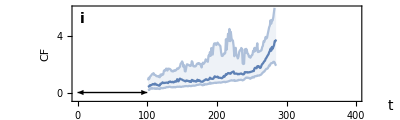

```mathematica
coherSeriesPlot=ListPlot[{{tVals[[windowComps+1;;tcritTrun]],quantile25Coher}ᵀ,
{tVals[[windowComps+1;;tcritTrun]],quantile75Coher}ᵀ,{tVals[[windowComps+1;;tcritTrun]],medianCoher}ᵀ},
Joined->True,
PlotStyle->{Lighter[TMBcolours⟦1⟧,0.5],Lighter[TMBcolours⟦1⟧,0.5],TMBcolours⟦1⟧},
Filling->{{1->{3}},{2->{3}}},
LabelStyle->14,
Frame->{{True,False},{True,True}},
PlotRange->{{0,tmax},{-0.5,6}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameLabel->{{"CF",""},{"Time",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{{0,2,4,6},Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3,
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Arrow[{Scaled[{0,arHeight},{0,0}],Scaled[{0,arHeight},{windowComps,0}]}],
(*Text[Style["×10^-3",14,TMBcolours[[1]]],indexPos]*)
Text[Style["t",14],Scaled[{1.1,-0.05}]],
Text[Style["i",14,Bold],Scaled[labelLetterPos]]}]
```

#### Compute AIC weights from power spectra

```mathematica
pSpecSeries//Dimensions
```

{100,185,2,41}

```mathematica
?TBFitSpec
```

TBFitSpec[pSpec] fits the unimodal and bimodal power specrums that occur preceding a Fold and a Hopf bifurcation respectively to the provided power spectrum.
pSpec = {freqVals,powerVals}
Outputs {hopfAICweight,rSquaredRatio,cUni,λUni,cBi,λBi,ω0Bi}
AIC weights can be interpreted as the probability that the fitted model is the best model (in the AIC sense)
RSquared ratio is R^2 of Fold divided by R^2 of Hopf
c is the noise parameter
λ is the absolute value of the dominant eigenvalue
ω0 is the intrinsic frequency
as found in each of the fitted power spectra

```mathematica
Dimensions[pSpecSeries][[2]]
```

185

```mathematica
Quiet[TBFitSpec[pSpecSeries[[1,150]]]]
```

{1.,0.447575,553669.,1044.99,0.170432,-0.280192,2.98455}

```mathematica
(*(* compute AIC weights - LONG SIMULATION *)
aicWeightSeriesTrun=Monitor[
Table[Quiet[TBHopfAIC[pSpecSeries[[i,j]]]],{i,1,numRealisations},{j,1,Dimensions[pSpecSeries][[2]]}],
{ProgressIndicator[i,{1,numRealisations}],ProgressIndicator[j,{1,Dimensions[pSpecSeries][[2]]}]}];*)
```

```mathematica
(*(* export AIC weights *)
Export["data/sim_data/aicWeightsTrun.csv",aicWeightSeriesTrun];*)
```

```mathematica
(* import aic weights *)
aicWeightSeriesTrun=Import["data/sim_data/aicWeightsTrun.csv"];
```

```mathematica
aicWeightSeriesTrun//Dimensions
```

{100,185}

```mathematica
(* a plot averaged over simulations *)
meanAICSeries=Mean[aicWeightSeriesTrun];
devAICSeries=StandardDeviation[aicWeightSeriesTrun];
```

```mathematica
(* quantiles *)
quantile25aicWeights=Quantile[aicWeightSeriesTrun,0.25];
medianaicWeights=Quantile[aicWeightSeriesTrun,0.5];
quantile75aicWeights=Quantile[aicWeightSeriesTrun,0.75];
```

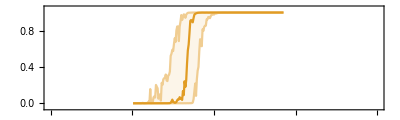

```mathematica
aicWeightSeriesPlot=ListPlot[{{tVals[[windowComps+1;;tcritTrun]],quantile25aicWeights}ᵀ,
{tVals[[windowComps+1;;tcritTrun]],quantile75aicWeights}ᵀ,{tVals[[windowComps+1;;tcritTrun]],medianaicWeights}ᵀ},
Joined->True,
PlotStyle->{Lighter[TMBcolours⟦2⟧,0.5],Lighter[TMBcolours⟦2⟧,0.5],TMBcolours⟦2⟧},
Filling->{{1->{3}},{2->{3}}},
LabelStyle->14,
PlotRange->{{0,tmax},{-0.05,1.05}},
Frame->{{False,True},{True,True}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameLabel->{{"","w_AIC"},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,All},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->400,
AspectRatio->0.3]
```

```mathematica
psdMetricTrunPlot=Overlay[{coherSeriesPlot,aicWeightSeriesPlot}]
```

-Graphics--Graphics-

## Bifurcation Diagram (truncated growth)

Deterministic model is
N_(t+1)=N_t e^(r(1-N_t/K))-F N_t^2/(N_t^2+h^2)

### Specifications

```mathematica
(* Import data *)
rawdata=Import["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_16/fish_project/bifurcation/fish_trun.dat"];

(* plotting spec *)
lt=0.0075; (* line thickness *)
ls=10; (* label size *)
ps=0.03; (* point size *)
imgs=400; (* image size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
plRange={{0,3},{0,20}}; (* plot range *)
(*frLabel={"F","N"}; (* frame label *)*)
(*aRatio=2/3; (* aspect ratio *)*)

(* Colors of equilibrium lines in order as above *)
eqColors={Black,{Black,Dashing[{1lt,3lt}]},Black,{Red,Dashing[{lt,3lt}]}};
```

### Line Plot

```mathematica
(* Split up high and low points into seperate rows *)
fulldata=Join[rawdata[[;;,{1,2,4,5}]],rawdata[[;;,{1,3,4,5}]]]//DeleteDuplicates;
(* Data using t instead of F *)
rbifVals=fulldata[[;;,1]];
tbifVals=(rbifVals-rl)*tmax /(rh-rl);
fulldataT=ReplacePart[Transpose[fulldata],1->tbifVals]//Transpose;
```

```mathematica
(* Stability type of point i *)
stabType=fulldataT[[;;,3]];
```

```mathematica
numPoints=Length[fulldataT];
```

```mathematica
(* Find rows where stability has changed (bif rows) *)
bifPts={1};
i=1;
While[i<numPoints,
s=stabType[[i]];
If[s==stabType[[i+1]],i=i+1,
bifPts=Append[bifPts,i+1];i=i+1]]
```

```mathematica
(* Split up fulldata into node sections *)
nodeSections=Append[
Table[fulldataT[[bifPts⟦i⟧;;bifPts⟦i+1⟧]],{i,1,Length[bifPts]-1}], (* If line join jumps to other curves, vary this *)
fulldataT⟦Last[bifPts];;⟧];

(* Ignore sections with two points (they are the result of end points *)
nodeSections=DeleteCases[DeleteCases[nodeSections,{_}],{}];
```

```mathematica
(* Adjust certain branches *)
nodeSections[[8]]=Cases[nodeSections[[8]],{x_,_,_,_}/; x<999] ; 
nodeSections[[10]]=Cases[nodeSections[[10]],{x_,_,_,_}/; x<999];
(* had to seperate out branches for plotting purposes *)
```

```mathematica
numBranches=Length[nodeSections];
```

```mathematica
(* Stabilty of sections *)
stab=Table[nodeSections[[i,1,3]],{i,1,numBranches}]
```

{2,1,2,1,2,1,2,1,2,1}

```mathematica
(* Take relevant branches of node sections *)
delList={5,7};
branchesNums=Complement[Range[1,numBranches],delList]
```

{1,2,3,4,6,8,9,10}

```mathematica
(* Color vector *)
colorScheme=eqColors[[stab[[branchesNums]]]];
```

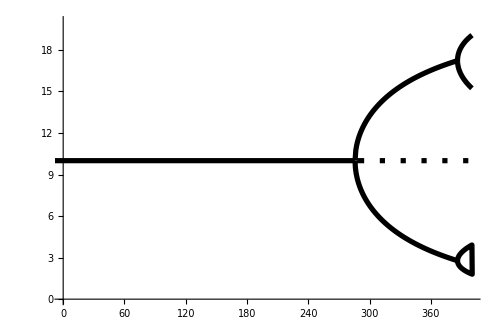

```mathematica
(* Make plot *)
bifPlotTrun=ListCurvePathPlot[Join[nodeSections[[branchesNums]]],
PlotStyle->Transpose[{colorScheme,ConstantArray[Thickness[lt],Length[colorScheme]]}],
LabelStyle->font,
InterpolationOrder->None,
PlotRange->{{0,tmax},{0,20}},
Axes->{True,True},
ImageSize->{500,300},
AspectRatio->2/3,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}
]
```

### Incorporate bif diagram with Simulation

```mathematica
lineStyle={TMBcolours[[4]],Opacity[1]};
arLength=windowComps;
sqCenter=10;
sqHeight=2.5;
```

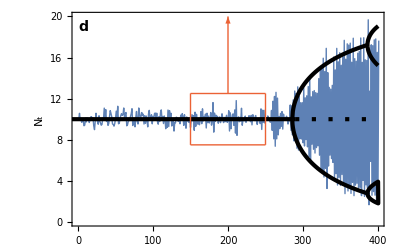

```mathematica
(* Incorporate with simulation *)
figBifTrajTrun=Show[{plotSingleTrun,bifPlotTrun},
PlotRange->{{0,tmax},{0,20}},
LabelStyle->14,
Frame->{{True,True},{True,True}},
AxesLabel->None,
ImagePadding->{{padLeft,padRight},{padBottom-5,padTop-5}},
FrameLabel->{{"N_t",""},{"",""}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
ImageSize->imgs,
Epilog->{Text[Style["d",14,Bold],Scaled[{0.035,0.93}]],
Directive[lineStyle],
Line[{{psdTime,-sqHeight+sqCenter},{psdTime,sqHeight+sqCenter}}],
Line[{{psdTime-windowComps,-sqHeight+sqCenter},{psdTime-windowComps,sqHeight+sqCenter}}],
Line[{{psdTime-windowComps,sqHeight+sqCenter},{psdTime,sqHeight+sqCenter}}],
Line[{{psdTime-windowComps,-sqHeight+sqCenter},{psdTime,-sqHeight+sqCenter}}],
Arrow[{{psdTime-windowComps/2,sqHeight+sqCenter},{psdTime-windowComps/2,20}}]}
]
```

## Figure Construction

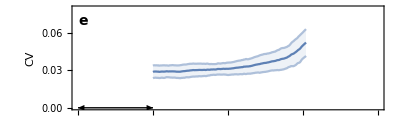
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics--Graphics- | -Graphics--Graphics-

```mathematica
figFishEws=Grid[{{psdAvExp,psdAvTrun},{figBifTrajExp,figBifTrajTrun},{cvPlotExp,cvPlotTrun},{acPlotLagsExp,acPlotLagsTrun},{psdMetricExpPlot,psdMetricTrunPlot}},Spacings->{0,-0.6}]
```

```mathematica
(*Export["figures/ews_ricker_trans.png",figFishEws,ImageResolution->200];*)
```